```mathematica
ClearAll[MPLColorMap];
<<"http://pastebin.com/raw/pFsb4ZBS";
vgreen1=MPLColorMap["Viridis"][0.6];
vgreen2 = MPLColorMap["Viridis"][1];
```

```mathematica
tCurve = ParametricPlot[{x,Sin[1/x]},{x,0,1}, PlotStyle->{Black}, PlotLabel->"Topologist's Sine Curve"];
```

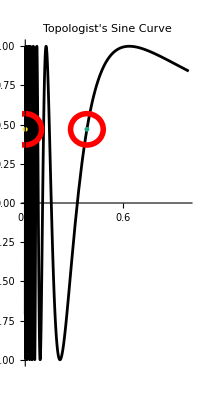

```mathematica
p1 = Graphics[{Thickness[0.05],vgreen1, Disk[{0.377,0.47},0.015]}];
p2 = Graphics[{Thickness[0.05],vgreen2, Disk[{0.,0.47},0.015]}];
u1 = Graphics[{Thickness[0.01],Red,Circle[{0.377,0.47},0.1]}];
u2 = Graphics[{Thickness[0.01],Red,Circle[{0.,0.47},0.1]}];
tCurvePlot = Show[tCurve,p1,p2,u1, u2]
```

```mathematica
Export["TSin_Curve.png",tCurvePlot]
```

TSin_Curve.png